```mathematica
soleqsecondogrado=Solve[ a x^2 + b x + c == 0 , x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
x/. soleqsecondogrado
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

```mathematica
x
```

x

```mathematica
(*"vettorializzo le soluzioni" in una lista *)
```

```mathematica
x1= x/. soleqsecondogrado[[1]]
```

(-b-√(b^2-4 a c))/(2 a)

```mathematica
x1
```

(-b-√(b^2-4 a c))/(2 a)

```mathematica
NIntegrate[Exp[-x^2],{x,-1,1}]
```

1.49365

```mathematica
Integrate[ Exp[ -x^2] , {x,-1,1}]
```

√π Erf[1]

```mathematica
Integrate[ Exp[ -x^2] , {x,-a,a}]
```

√π Erf[a]

```mathematica
int1[a_] = Integrate[ Exp[ -x^2] , {x,-a,a}]
```

√π Erf[a]

```mathematica
int1[b]
```

√π Erf[b]

```mathematica
int2[a_] = NIntegrate[ Exp[ -x^2] , {x,-a,a}]
```

NIntegrate[Exp[-x^2],{x,-a,a}]

```mathematica
int2[a_] := NIntegrate[ Exp[ -x^2] , {x,-a,a}]
```

```mathematica
int2[10]
```

1.77245

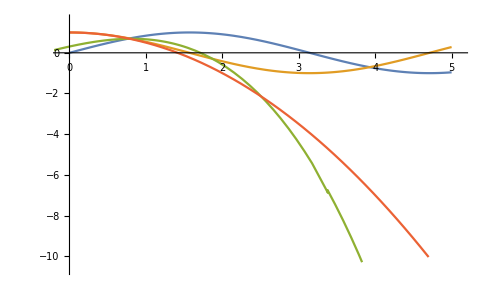

```mathematica
Plot[{Sin[x],Cos[x],x-x^3/6,1-x^2/2},{x,0,5}]
```

```mathematica
Plot3D[Sin[x^2+y^2],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
??Plot3D
```

Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}] generates a three-dimensional plot of f as a function of x and y. 
Plot3D[{f_1,f_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several functions. 
Plot3D[…,{x,y}∈reg] takes variables {x,y} to be in the geometric region reg.

Attributes[Plot3D]={Protected,ReadProtected}

```mathematica
Options[Plot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClippingStyle→Automatic,ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Opacity[0.5],FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,ScalingFunctions→None,SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

```mathematica
g3= Plot3D [Sin[x^2+y^2] , {x,-3,3} , {y,-3,3}, PlotPoints->50]
```

-Graphics3D-

```mathematica
f[a_,b_,c_]:=Show[g3,ViewPoint->{a,b,c}]
(*Coseni direttori dell'angolo di visione del grafico*)
```

```mathematica
f[1,1,1]
```

-Graphics3D-

```mathematica
f[0,1,1]
```

-Graphics3D-

```mathematica
f[1,0,0]
```

-Graphics3D-

```mathematica
f[0,0,-1]
```

-Graphics3D-

```mathematica
??Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

Attributes[Show]={Protected,ReadProtected}

```mathematica
final=f[0,1,0];
```

```mathematica
Export["final.jpg",final,"JPEG"]
```

final.jpg

```mathematica
SystemOpen["final.jpg"]
```

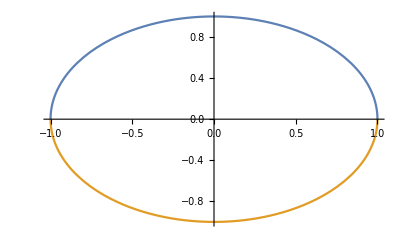

```mathematica
Plot[ {Sqrt[1-x^2],-Sqrt[1-x^2]},{x,-1,1}]
```

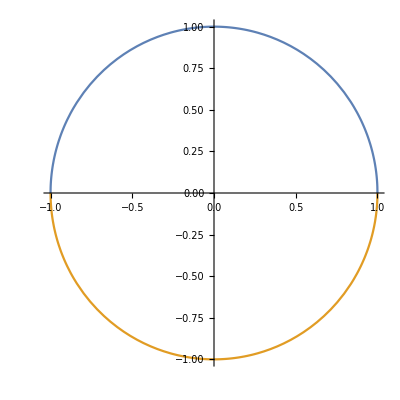

```mathematica
Plot[ {Sqrt[1-x^2],-Sqrt[1-x^2]},{x,-1,1}, AspectRatio->1]
```

```mathematica
??ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions. 
ParametricPlot[…,{u,v}∈reg] takes parameters {u,v} to be in the geometric region reg.

Attributes[ParametricPlot]={HoldAll,Protected,ReadProtected}
 
Options[ParametricPlot]={AlignmentPoint→Center,AspectRatio→Automatic,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→Automatic,MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

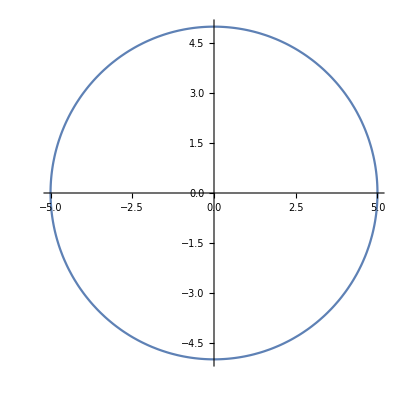

```mathematica
ParametricPlot[r=5; { r Cos[th] , r Sin[th]} , {th,0,2 Pi} , AspectRatio->1]
```

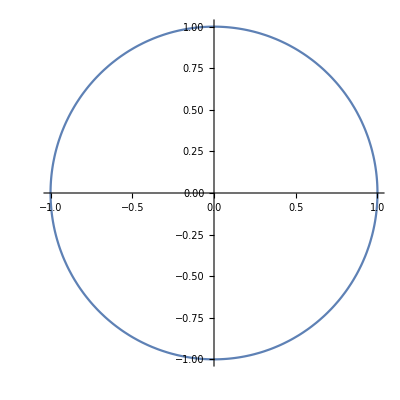

```mathematica
ParametricPlot[ { Cos[th] , Sin[th]} , {th,0,2 Pi} , AspectRatio->1]
```

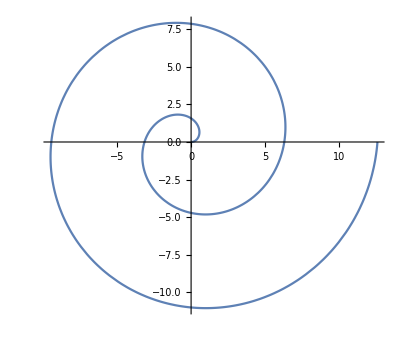

```mathematica
ParametricPlot[ r= th; {r Cos[th] , r Sin[th]} , {th, 0 , 4 Pi} ]
```

```mathematica
ParametricPlot3D[ r=Sqrt[3];{ r Sin[th] Sin[phi] ,  r Sin[th] Cos[phi] ,  r Cos[th]} , {th , 0, Pi},{phi, 0 , 2 Pi}]
```

-Graphics3D-

```mathematica
f[x_]:= Which[ x<0 , -1 , x≥0 && x<2 Pi , x ^2-1 , x≥2 Pi , Sin[x]]
```

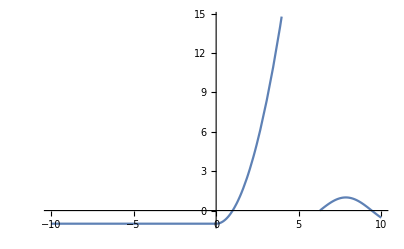

```mathematica
Plot[ f[x] , {x ,-10,10}]
```

viene valutata la prima condizione che restituisce true

funzione definita per casi